# QEA - Differential Equations in Class

```mathematica
SetDirectory@NotebookDirectory[];
<<"../General.m"
```

## ConceptualQuestions1

```mathematica
With[{context="conceptualquestions1`"},If[Context[] ≠ context,Begin[context]]];Dynamic[Refresh[Context[],UpdateInterval->1]]
```

```mathematica
With[{},
sol=DSolveValue[ψ'[t]==−ψ[t]+Cos[ψ[t]],ψ[t],t]
]
```

InverseFunction[∫_1^#1 1/(-Cos[K[1]]+K[1])ⅆK[1]&][-t+C[1]]

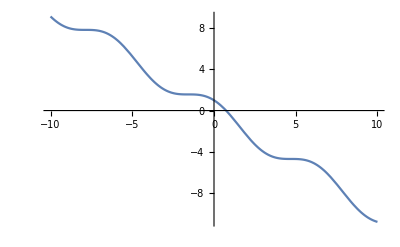

```mathematica
Plot[−ψ+Cos[ψ],{ψ,-10,10}]
```

```mathematica
With[{context="conceptualquestions1`"},If[Context[]==context,End[],"Not in context"]]
```

conceptualquestions1`

```mathematica
makeTemplate["conceptualquestions2"]
```

## conceptualquestions2

```mathematica
With[{context="conceptualquestions2`"},If[Context[] ≠ context,Begin[context]]];Dynamic[Refresh[Context[],UpdateInterval->1]]
```

```mathematica
With[{context="conceptualquestions2`"},If[Context[]==context,End[],"Not in context"]]
```

Not in context

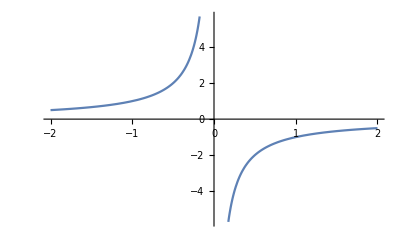

```mathematica
Table[Plot[-x^n,{x,-2,2}],{n,{-1}}]
```

```mathematica
makeTemplate["October24Inclass"]
```

## October24Inclass

```mathematica
With[{context="october24inclass`"},If[Context[] ≠ context,Begin[context]]];Dynamic[Refresh[Context[],UpdateInterval->1]]
```

```mathematica
With[{V=9,R=50,Troom=26.8,h=0.0364},
de={T'[t]==1/Cp(V^2/R-h(T[t]- Troom))};
initialConditions={T[0]==Troom};

sol=DSolveValue[Join[de,initialConditions],T[t],t]
]
```

71.3055 ⅇ^(-(0.0364 t)/Cp) (-0.624152+1. ⅇ^((0.0364 t)/Cp))

```mathematica
field=VectorPlot[{de},{},{}];
```

```mathematica
Plot[sol,{t,0,20},PlotRange->All]
```

-Graphics-

```mathematica
With[{Cp=10,V=9,R=50,Troom=70+273,h=10},
de={T'[t]==1/Cp(V^2/R-h(T[t]- Troom))};

N@de/.T[t]->20
]
```

{T'[t]==323.162}

```mathematica
W
```

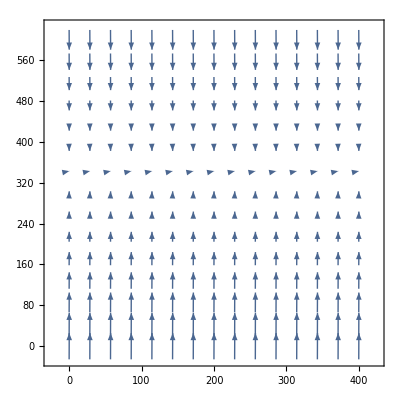

```mathematica
With[{Cp=10,V=9,R=50,Troom=70+273,h=10},
de=1/Cp(V^2/R-h(T- Troom));
VectorPlot[{1,de},{t,0,400},{T,0,600}]
]
```

```mathematica
With[{Cp=10,V=9,R=50},
Solve[Cp 0==(V^2/R-h(713.6/10- 268/10)),h]
]
```

{{h→0.0363555}}

```mathematica
data=Import["temprun.csv","CSV"];
x=Transpose[data][[1]]-Min[Transpose[data][[1]]];
y=Transpose[data][[2]]*100;
```

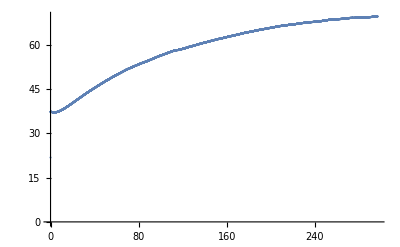

```mathematica
ListPlot[Transpose@{x,y}]
```

```mathematica
FindFit[Transpose@{x,y},71.30549450549451 ⅇ^(-(0.0364 t)/Cp) (-0.6241523856491186+1. ⅇ^((0.0364 t)/Cp)),{Cp},t]
```

{Cp→3.22476}

```mathematica
With[{context="october24inclass`"},If[Context[]==context,End[],"Not in context"]]
```

october24inclass`